## Functions

```mathematica
ClearDominates[]:=Block[{},
DownValues[Dominates]={};
Dominates[p_,q_,m_]:=Dominates[p,q,m]=Block[{pans,qans},
pans=#[p]&/@m;
qans=#[q]&/@m;
And@@{Or@@(#⟦1⟧<#⟦2⟧&/@Transpose[{pans,qans}]),
And@@(#⟦1⟧≤#⟦2⟧&/@Transpose[{pans,qans}])}
]
];
ClearDominates[];
```

```mathematica
ClearDominates[]:=Block[{},
DownValues[Dominates]={};
Dominates[p_,q_,m_]:=Dominates[p,q,m]=Block[{pans,qans},
pans=#[p]&/@m;
qans=#[q]&/@m;
And@@(#⟦1⟧≤#⟦2⟧&/@Transpose[{pans,qans}])
]
];
ClearDominates[];
```

```mathematica
Clear[FastNonDominatedSort];
FastNonDominatedSort[Pin_,m_]:=Block[{F,n,H,i,S},
F[1]={};
Map[Block[{p=#},
Map[Block[{q=#},
n[p]=0;
If[Dominates[p,q,m],
AppendTo[S[p],q],
If[Dominates[q,p,m],
n[p]=n[p]+1;
]];
]&,Pin];
If[n[p]==0,
AppendTo[F[1],p]
];
]&,Pin];
i=1;
While[Length[F[i]]>0,
H={};
Map[Block[{p=#},
Map[Block[{q=#},
n[q]=n[q]-1;
If[n[q]==0,
AppendTo[H,q]];
]&,S[p]]
]&,F[i]];
i++;
F[i]=H;
];
F[#]&/@Range[i-1]
]
```

```mathematica
CrowdingDistanceAssignment[Iin_,m_]:=Module[{Isorted,l,I,Iorder,Idistance},
I=Iin;
l=Length[I];
Set[Idistance[#],0]&/@Range[l];
Map[Block[{n=#},
Iorder=Ordering[I,All,n[#1]<n[#2]&];
Idistance[Iorder⟦1⟧]=Idistance[Iorder⟦-1⟧]=∞;
(*Idistance[0]=Idistance[l]=∞;*)
Map[Block[{i=#},
Idistance[i]=Idistance[i]+(n[I⟦Iorder⟦i+1⟧⟧]-n[I⟦Iorder⟦i-1⟧⟧])^1;
]&,Range[2,l-1]];
]&,m];
Idistance[Iorder⟦#⟧]&/@Range[l]
]
```

```mathematica
CrowdingDistanceAssignment[Iin_,m_]:=Module[{IIsorted,l,I,Iorder,Idistance},
I=Iin;
$I=I;
l=Length[I];
Set[Idistance[#],0]&/@Range[l];
Map[Block[{n=#},
Iorder=Ordering[I,All,n[#1]<n[#2]&];
Idistance[Iorder⟦1⟧]=Idistance[Iorder⟦-1⟧]=∞;
]&,m];
clusters=FindClusters[Block[{a=#},Map[#[a]&,m]]&/@I];
standardclusters=If[Length[#]>1,StandardDeviation[#]/Length[#],∞]&/@clusters;
MapIndexed[Idistance[#2⟦1⟧]+=Total[standardclusters⟦Position[clusters,Block[{a=#},Map[#[a]&,m]]]⟦1,1⟧⟧]&,I];
Idistance[#]&/@Range[l]
]
```

```mathematica
Ordering[{10,1,5}]
```

```mathematica
DominationRank[P_List,m_List]:=Block[{P2},
Map[Block[{p=#},
P2=Map[Block[{q=#},
Dominates[q,p,m]
]&,P];
Count[P2,True]
]&,P]
]
```

```mathematica
CrowdedComparisonOperator[i_List,j_List]:=Block[{},
(i⟦3⟧<j⟦3⟧)||((i⟦3⟧==j⟦3⟧)&&(i⟦2⟧>j⟦2⟧))||i⟦2⟧==∞
]
```

#### Random Numbers

```mathematica
RandomUnion[no_]:=Block[{randlist=Range[no],rand,randno},Table[rand=RandomInteger[{1,Length[randlist]}];randno=randlist⟦rand⟧;randlist=Drop[randlist,{rand}];randno,{no}]]
```

```mathematica
RandomUnion[no_,subno_]:=Block[{randlist=Range[no],rand,randno},Table[rand=RandomInteger[{1,Length[randlist]}];randno=randlist⟦rand⟧;randlist=Drop[randlist,{rand}];randno,{subno}]]
```

```mathematica
randomnumbers[number_]:=(SeedRandom[];RandomReal[{0,1},number])
```

```mathematica
bin6[b_,c_]:=b[[#]]&/@Split[Ordering[c],c[[#1]]==c[[#2]]&];
```

#### SelectforCrossover

```mathematica
Clear[SelectforCrossoverTournament]
```

```mathematica
SelectforCrossoverTournament[list_,pc_Integer:2,m_]:=Block[{rnos,numbers,breeding={},crowd,dom,sortingdata},
numbers=Length[list];
While[Length[breeding]<numbers,
rnos=RandomInteger[{1,numbers},{pc}];
crowd=CrowdingDistanceAssignment[list⟦rnos⟧,m];
dom=DominationRank[list⟦rnos⟧,m];
sortingdata=Transpose[{rnos,crowd,dom}];
AppendTo[breeding,Sort[sortingdata,CrowdedComparisonOperator]⟦1,1⟧];
];
breeding]
```

```mathematica
Clear[SelectforCrossoverUniform];
SelectforCrossoverUniform[list_,pc_:0.4,m_]:=Block[{breeding={},numbers,nobreeding,crowd},
numbers=Length[list];
crowd=CrowdingDistanceAssignment[list,m];
dom=DominationRank[list,m];
probabilitylist=Rest[FoldList[Plus,0,#/Total[#]&[(crowd+1/.{∞->2Max[Select[crowd,#<∞&]]})*(Length[list]-dom)]]];
nobreeding=Length[Select[RandomReal[{0,1},{numbers}],#<pc&]];
If[OddQ[nobreeding],
If[nobreeding<numbers&&RandomReal[{0,1}]<0.5,
nobreeding=nobreeding+1,
nobreeding=nobreeding-1
]
];
While[Length[Union[breeding]]<nobreeding,
If[RandomReal[{0,1}]<pc,
AppendTo[breeding,Block[{prob=#},Position[probabilitylist,Select[probabilitylist,prob<#&]⟦1⟧]⟦1,1⟧]&[RandomReal[{0,1}]]]
]];
Union[breeding]
]
```

```mathematica
RandomPermutation
```

```mathematica
Clear[SelectforCrossoverAll];
SelectforCrossoverAll[list_]:=Block[{breeding={},numbers,nobreeding,crowd},
RandomSample[Range[20],20]
]
```

#### Crossover

```mathematica
outsiderange[value_,start_,end_]:=Which[(2start-value)>end,end,(2end-value)<start,start,value<start,outsiderange[2start-value,start,end],value>end,outsiderange[2end-value,start,end],value≥start&&value≤end,value]
```

```mathematica
crossovermethods={"Biased","Interpolated","SBX"}
```

```mathematica
InvDistC[x_,n_]:=Switch[Random[Integer,{0,1}],0,1^(1/(1+n)) x^(1/(1+n)),1,Abs[ 2^(-1/(1+n))(0.5-1 x)^(-1/(1+n))]]
```

```mathematica
CrossoverSBX[datalistin_,crosslist_,start_,end_]:=Block[{datalist=datalistin,lengths,crossingpositions,randomcrossingpositions,pairedcrossingpositions,crosseddata},
crossingpositions=crosslist;
randomcrossingpositions=RandomUnion[Length[crossingpositions]];
pairedcrossingpositions=Partition[crossingpositions⟦randomcrossingpositions⟧,2];
crosseddata=Block[{chrom=datalistin⟦#⟧},SBX[chrom]]&/@pairedcrossingpositions;
((datalist=ReplacePart[datalist,#⟦1⟧->#⟦2⟧])&/@#)&/@MapThread[Transpose[{##}]&,{pairedcrossingpositions,crosseddata}];
CheckRange[datalist,start,end]]
```

```mathematica
SBX[inputin_]:=Block[{absmeans,relmeans,orders,a,input=inputin,betas},
absmeans=Mean[#]&/@Transpose[input];
relmeans=Mean[#-Min[#]]&/@Transpose[input];
orders=Ordering[#]&/@Transpose[input];
betas=InvDistC[Random[Real,{0,1}],$betafactor];
a=Switch[Random[Integer,{0,1}],1,{#⟦1⟧-(#⟦2⟧*betas),#⟦1⟧+(#⟦2⟧*betas)},0,#⟦4⟧]&/@Transpose[{absmeans,relmeans,orders,Transpose[input]}];
Transpose[a]
]
```

```mathematica
CheckRange[data_,start_,end_]:=
outsiderange[Sequence@@#]&/@Transpose[{#,If[ListQ[start],start,Table[start,{Length[#]}]],If[ListQ[end],end,Table[end,{Length[#]}]]}]&/@data
```

```mathematica
CrossoverBiased[datalistin_,crosslist_,start_,end_]:=Block[{datalist=datalistin,lengths,crossingpositions,randomcrossingpositions,pairedcrossingpositions,crosseddata},
crossingpositions=crosslist;
randomcrossingpositions=RandomUnion[Length[crossingpositions]];
pairedcrossingpositions=Partition[crossingpositions⟦randomcrossingpositions⟧,2];
(*Print[pairedcrossingpositions];*)
crosseddata=Transpose[Module[{chrom=datalistin⟦#⟧},If[RandomReal[{0,1}]<$parentbias,#,Reverse[#]]&/@Transpose[chrom]]]&/@pairedcrossingpositions;
(*Print[MapThread[Transpose[{##}]&,{pairedcrossingpositions,crosseddata}]];*)
((datalist=ReplacePart[datalist,#⟦1⟧->#⟦2⟧])&/@#)&/@MapThread[Transpose[{##}]&,{pairedcrossingpositions,crosseddata}];datalist]
```

```mathematica
CrossoverInterpolated[datalistin_,crosslist_,start_,end_]:=Block[{datalist=datalistin,lengths,crossingpositions,randomcrossingpositions,pairedcrossingpositions,crosseddata,p},
crossingpositions=crosslist;
randomcrossingpositions=RandomUnion[Length[crossingpositions]];
pairedcrossingpositions=Partition[crossingpositions⟦randomcrossingpositions⟧,2];
(*Print[pairedcrossingpositions];*)
crosseddata=Transpose[Module[{chrom=datalistin⟦#⟧},{#⟦1⟧(p=RandomReal[{-1,1}])+(1-p)#⟦2⟧,#⟦2⟧(p=RandomReal[{-1,1}])+(1-p)#⟦1⟧}&/@Transpose[chrom]]]&/@pairedcrossingpositions;

((datalist=ReplacePart[datalist,#⟦1⟧->#⟦2⟧])&/@#)&/@MapThread[Transpose[{##}]&,{pairedcrossingpositions,crosseddata}];CheckRange[datalist,start,end]]
```

#### Mutate

```mathematica
mutationmethods={"Gaussian","Scaled"}
```

```mathematica
MutateGaussian[value_,start_,end_,mutationsize_]:=outsiderange[value+Random[NormalDistribution[0,mutationsize]],start,end]
```

```mathematica
MutateScaled[value_,start_,end_,mutationsize_]:=outsiderange[value*RandomReal[{-mutationsize,mutationsize}],start,end]
```

```mathematica
Mutate[list_,mr_,start_,end_,mutationmethod_,mutationsize_]:=Block[{},
Module[{data=Transpose[{#,If[ListQ[start],start,Table[start,{Length[#]}]],If[ListQ[end],end,Table[end,{Length[#]}]],If[ListQ[mutationsize],mutationsize,Table[mutationsize,{Length[#]}]]}]},
If[RandomReal[{0,1}]<mr,mutationmethod[Sequence@@##],#⟦1⟧]&/@data]&/@list
]
```

```mathematica
GetIterationNumber[]:=iterationno
```

### Final GA

```mathematica
createPopulation[ranges_List,nochroms_,dims_]:=Block[{},
If[Dimensions[ranges]⟦1⟧>2&&Dimensions[ranges]⟦1⟧==dims,
Transpose[RandomReal[#,{nochroms}]&/@ranges],
RandomReal[ranges,{nochroms,dims}]
]
]
```

```mathematica
RoundNumbers[numbers_List,dec_]:=Block[{round},
round=10^-dec;
N[Round[numbers,round]]
]
```

```mathematica
RealNDSGA[dims_,nochroms_,ranges_,functions_,nogenerations_,opts___Rule]:=Block[{PopCombined,PopSelected,finaldata,mutatedpop,breeding,crossedpop,pop1,pop2,start,end,tournamentno,selectprob,decimalplaces,mutationsize,mr,pop3,crowd,finishedsorting},
tournamentno=Global`TournamentNumber/.{opts}/.{Global`TournamentNumber->2};
selectprob=Global`SelectionProbability/.{opts}/.{Global`SelectionProbability->0.5};
$betafactor=Global`BetaFactor/.{opts}/.{Global`BetaFactor->1};
mr=Global`MutationRate/.{opts}/.{Global`MutationRate->0.1};
mutationsize=Global`MutationSize/.{opts}/.{Global`MutationSize->0.1};
decimalplaces=Global`DecimalPlaces/.{opts}/.{Global`DecimalPlaces->3};
$parentbias=Global`ParentBias/.{opts}/.{Global`ParentBias->0};
pop1=createPopulation[ranges,nochroms,dims];
pop2=createPopulation[ranges,nochroms,dims];
start=If[Dimensions[ranges]⟦1⟧>2,ranges⟦All,1⟧,ranges⟦1⟧];
end=If[Dimensions[ranges]⟦1⟧>2,ranges⟦All,2⟧,ranges⟦2⟧];
ClearDominates[];(* Clear Definitions of Dominates *)
Generations=RoundNumbers[{pop1,pop2},decimalplaces];
SelectedGenerations={};
Do[
finishedsorting=0;
PopCombined=Join[Generations⟦-2⟧,Generations⟦-1⟧];
PopFNDS=FastNonDominatedSort[PopCombined,functions];
PopSelected=Block[{sortingdata,sorteddata,PopNew,crom,dom},
PopNew={};
If[Length[Flatten[PopNew,1]]<nochroms,
PopNew=Join[PopNew,{#}];
If[Length[Flatten[PopNew,1]]≥nochroms&&finishedsorting==0,
finishedsorting=1;
crowd=CrowdingDistanceAssignment[Last[PopNew],functions];
dom=DominationRank[Last[PopNew],functions];
sortingdata=Transpose[{Last[PopNew],crowd,dom}];
sorteddata=Sort[sortingdata,CrowdedComparisonOperator];
(*IF Comparison Sorting ALL of popnew
finaldata=Take[sorteddata,nochroms]⟦All,1⟧;
*)
finaldata=Flatten[Join[Most[PopNew],{Take[sorteddata,nochroms-Length[Flatten[Most[PopNew],1]]]⟦All,1⟧}],1];
]
]&/@PopFNDS;
If[Dimensions[finaldata]=!={nochroms,dims},Print[finaldata]];
finaldata
];
AppendTo[SelectedGenerations,PopSelected];
(*breeding=SelectforCrossoverTournament[PopSelected,tournamentno,functions];*)
breeding=SelectforCrossoverUniform[PopSelected,selectprob,functions];
(*breeding=SelectforCrossoverAll[PopSelected];*)
crossedpop=If[Abs[$parentbias]>0,
RoundNumbers[CrossoverBiased[PopSelected,breeding,start,end],decimalplaces],
RoundNumbers[CrossoverSBX[PopSelected,breeding,start,end],decimalplaces]];
mutatedpop=RoundNumbers[Mutate[crossedpop,mr,start,end,MutateScaled,mutationsize],decimalplaces];
AppendTo[Generations,mutatedpop];
,{nogenerations}]
]
```

## MOP4

```mathematica
Clear[f1base,f1,f2base,f2]
```

```mathematica
f1base=Compile[{{x,_Real,1}},Sum[(-10Exp[-0.2(x⟦i⟧^2+x⟦i+1⟧^2)^0.5]),{i,1,2}]];
f1[x_]:=f1[x]=f1base[x]
```

```mathematica
testdata=Flatten[Table[{i,j,k},{i,-5,5,0.25},{j,-5,5,0.25},{k,-5,5,0.25}],2];
```

```mathematica
AbsoluteTiming[f1[#]&/@testdata⟦All⟧;]
```

```mathematica
f2base=Compile[{{x,_Real,1}},Sum[Abs[x⟦i⟧]^0.8+5 Sin[x⟦i⟧]^3,{i,1,3}]];
f2[x_]:=f2[x]=f2base[x]
```

```mathematica
testdata=Flatten[Table[{i,j,k},{i,-5,5,0.25},{j,-5,5,0.25},{k,-5,5,0.25}],2];
```

```mathematica
AbsoluteTiming[f2[#]&/@testdata⟦All⟧;]
```

### Create Comparison Data

```mathematica
testdata=Flatten[Table[{i,j,k},{i,-5,5,0.1},{j,-5,5,0.1},{k,-5,5,0.1}],2];
```

```mathematica
ansdata=Select[{f1[#],f2[#]}&/@testdata,#⟦1⟧<-14&&#⟦2⟧<0&];
```

```mathematica
ComparisonPlot=ListPlot[ansdata,
PlotRange->{{-20,-14},{-12,0}},Frame->True]
```

### Run GA

```mathematica
RealNDSGA[3,10,{-5,5},{f1,f2},100]
```

```mathematica
Dynamic[If[Length[SelectedGenerations]>10,ListPlot[Map[Block[{d=#},Transpose@Map[Block[{f=#},Map[f[#]&,d]]&,functions]]&,SelectedGenerations⟦-1;;-1⟧],PlotRange->All,PlotRange->{{-20,-14},{-12,0}},Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]]
```

```mathematica
Histogram[#]&/@Map[Flatten,Transpose[Map[Transpose,SelectedGenerations⟦-10;;-1⟧]]]
```

```mathematica
.
```

```mathematica
Show[ComparisonPlot,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦All⟧,
PlotRange->{{-20,-14},{-12,0}},Frame->True,PlotStyle->(GrayLevel[1-#/Length[Generations]]&/@Range[Length[SelectedGenerations]])]]
```

## EC6

```mathematica
Clear[f1,f1base,f2,f2base]
```

```mathematica
f1base=Compile[{{x,_Real,1}},1-Exp[-4 x⟦1⟧] Sin[6π x⟦1⟧]^6];
f1[x_List]:=f1[x]=f1base[x]
```

```mathematica
f2base=Compile[{{x,_Real,1}},(g[x](1-(f1[x]/g[x])^2))];
f2[x_List]:=f2[x]=f2base[x]
```

```mathematica
g=Compile[{{x,_Real,1}},1+9(Total[Rest[x]]/9)^0.25];
```

### Run GA

```mathematica
RealNDSGA[10,200,{0,1},{f1,f2},200,BetaFactor->2,MutationRate->0.1,MutationSize->0.05]
```

```mathematica
ListPlot[FindClusters[{f1[#],f2[#]}&/@SelectedGenerations⟦-1⟧]]
```

```mathematica
Dynamic[If[Length[SelectedGenerations]>10,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,PlotRange->All,Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]]
```

```mathematica
aniplots=Block[{no=#},ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦Range[no-10,no]⟧,PlotRange->{{0.28,1},{0,5}},Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]&/@Range[11,60,1];
```

```mathematica
Directory[]
```

```mathematica
Export["NDSGA_In_Action.gif",aniplots]
```

```mathematica
ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦1;;-1⟧,
PlotRange->{{0.28,1},{0,1.4}},Frame->True,PlotStyle->{Black}]
```

## EC4

```mathematica
Clear[f1,f2,g]
```

```mathematica
f1[x_List]:=f1[x]=x⟦1⟧
```

```mathematica
f2[x_List]:=f2[x]=(g[x](1-√(x⟦1⟧/g[x])))//N
```

```mathematica
g=Compile[{{x,_Real,1}},(91+Sum[x⟦i⟧^2-10Cos[4π x⟦i⟧],{i,2,10}])]
```

### Run GA

testingdata$<crowdingfactor>$<tournament number>

```mathematica
Join[{{0,1}},Table[{-5,5},{9}]]
```

```mathematica
testingdata$2$1=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->1];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$2$2=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->2];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$2$3=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->3];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$3$1=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->1];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$3$2=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250,TournamentNumber->2];
SelectedGenerations]&/@Range[10];
```

```mathematica
testingdata$3$3=Block[{},
SeedRandom[#];
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250];
SelectedGenerations]&/@Range[10];
```

```mathematica
RealNDSGA[10,10,Join[{{0,1}},Table[{-5,5},{9}]],{f1,f2},250]
```

```mathematica
Dynamic[If[Length[SelectedGenerations]≥10,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,PlotRange->All,Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]]
```

```mathematica
ListPlot[{f1[#],f2[#]}&/@Flatten[#,1]&/@{
testingdata$2$1⟦All,-1⟧,testingdata$2$2⟦All,-1⟧,testingdata$2$3⟦All,-1⟧,
testingdata$3$1⟦All,-1⟧,testingdata$3$2⟦All,-1⟧,testingdata$3$3⟦All,-1⟧
},
PlotRange->{{0,1},{0,1.1}},Frame->True,PlotStyle->{Red,Blue,Black,Green,Purple,Brown}]
```

## KUR

```mathematica
Clear[f1,f1base,f2,f2base,f1n,f2n]
f1n=0;f2n=0;
```

```mathematica
f1[x_List]:=f1[x]=(f1n++;f1base[x]);
f1base=Compile[{{x,_Real,1}},Sum[(-10Exp[-0.2 √(x⟦i⟧^2+x⟦i+1⟧^2)]),{i,1,2}],CompilationTarget->"C"]
```

```mathematica
f2[x_List]:=f2[x]=(f2n++;f2base[x]);
f2base=Compile[{{x,_Real,1}},Sum[Abs[x⟦i⟧]^0.8+5 Sin[x⟦i⟧]^3,{i,1,3}],CompilationTarget->"C"]
```

```mathematica
Dynamic[f1n]
Dynamic[f2n]
```

### Create Comparison Data

testdata = Flatten[Table[{i, j, k}, {i, -5, 5, 0.1}, {j, -5, 5, 0.1}, {k, -5, 5, 0.1}], 2];

ansdata1 = {f1[#], f2[#]} & /@ testdata;

ansdata = Select[ansdata1, #[[1]] < -12 && #[[2]] < 0 &];

ComparisonPlot = ListPlot[ansdata, Frame -> True, PlotRange -> {{-20, -12}, {0, -11}}]

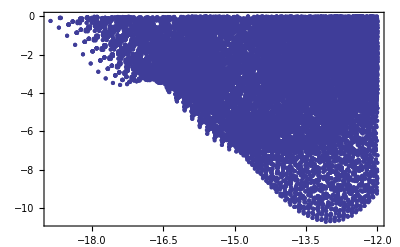

```mathematica
ComparisonPlot = -Graphics-
```

### Run GA

```mathematica
RealNDSGA[3,50,{-5,5},{f1,f2},200,BetaFactor->5,MutationRate->0.1,MutationSize->0.5]
```

```mathematica
Dynamic[If[Length[SelectedGenerations]≥10,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,PlotRange->All,Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]]
```

```mathematica
Show[ComparisonPlot,ListPlot[{f1[#],f2[#]}&/@#&/@SelectedGenerations⟦-10;;-1⟧,
PlotRange->{{-20,-14},{-12,1}},Frame->True,PlotStyle->(GrayLevel[1-#/10]&/@Range[10])]]
```

```mathematica
CrowdingDistanceAssignment[SelectedGenerations⟦20⟧,{f1,f2}]/.{∞->1}
```

```mathematica
Sort[Transpose[{{f1[#],f2[#]}&/@SelectedGenerations⟦-1⟧,CrowdingDistanceAssignment[SelectedGenerations⟦-1⟧,{f1,f2}]/.{∞->1}}],#1⟦2⟧>#2⟦2⟧&]
```

```mathematica
Graphics[{GrayLevel[1-#⟦2⟧],Point[{f1[#⟦1⟧],f2[#⟦1⟧]}]}&/@Transpose[{#,CrowdingDistanceAssignment[#,{f1,f2}]/.{∞->1}}]&/@SelectedGenerations⟦-10;;-1⟧,Frame->True]
```